```mathematica
S[x_]=4/Sqrt[10 Pi]Exp[-x^2/10];
Subscript[k, w][x_,ξ_]=Piecewise[{{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](x-ξ)],x<ξ}}];
Subscript[k, l][x_,ξ_]=Piecewise[{{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](x-ξ)],x<ξ}}];
var=Rationalize[{Subscript[α, w]->50.58,Subscript[β, w]->3.85/0.38,Subscript[η, w]->1/(0.38*10)*Q,Subscript[α, l]->192.2/(1.89*10),Subscript[β, l]->3.85/1.89,Subscript[η, l]->1/(1.89*10)*Q,Subscript[a, 0]->0.6,Subscript[a, 1]->0.38,M->0.38/1.89,Subscript[L, 0]->-1,Subscript[L, 1]->1}];
```

```mathematica
Subscript[T, 0][ξ_]:=-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,-∞,∞}]+Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,-∞,∞}]
Subscript[F, 0][ξ_]=Simplify[Subscript[T, 0][ξ]/.var];
```

```mathematica
N[Solve[Subscript[F, 0][0]==-1,Q]]
```

{{Q→548.681}}

```mathematica
Subscript[Q, min]=300;
Subscript[Q, max]=500;
n=2(Subscript[Q, max]-Subscript[Q, min])+1;
sols={};
Monitor[
For[i=0,i<n,i++,
tempQ={Q->Rationalize[Subscript[Q, min]+(Subscript[Q, max]-Subscript[Q, min])*i/(n-1),0]};
conds=Quiet[N[Subscript[F, 0][0]/.tempQ]<-1];
If[conds,M[x_]=Piecewise[{{Subscript[F, 0][x],x>=0},{Subscript[F, 0][-x],x<0}}/.tempQ];NUM=12001;points=Table[-6+12(i-1)/(NUM-1),{i,NUM}];
nSolution=N[Map[M, points]];sols=Join[sols,{{N[Round[Q/.tempQ,10^-10]],N[Round[Subscript[F, 0][0]/.tempQ,10^-10]],nSolution}}],Nothing];
],{N[i/n],N[Q/.tempQ]}]
Beep[]
```

```mathematica
Export["C:\\masterA GitHub\\Code\\Exponential\\Water\\1 - Ice.csv",sols,Format->Table];
```

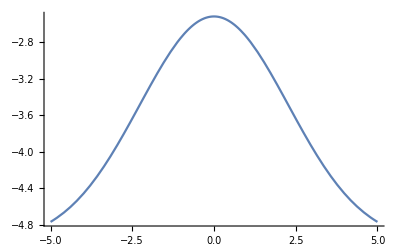

```mathematica
tempQ={Q->340};
M[x_]=Piecewise[{{Subscript[F, 0][x],x>=0},{Subscript[F, 0][-x],x<0}}/.tempQ];
Plot[M[x]/.tempQ,{x,-5,5}]
```

```mathematica
DiscretizedSolution = {};
points=2000;
dx=1/100;
Subscript[x, val]=Table[x*dx,{x,-2 *points,2*points-1}];
```

```mathematica
tempQ={Q->370};
sol=NSolve[{Subscript[eqn, 0]/.tempQ,Subscript[eqn, 1]/.tempQ,Subscript[eqn, 2]/.tempQ,Subscript[eqn, 3]/.tempQ},{Subscript[c, 0],Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]}];
sol=Join[sol[[1]],tempQ,var];
SetAttributes[M,Listable]
M[x_]=Piecewise[{{Subscript[F, 0][x]/.sol,x<Subscript[L, 0]/.sol},{Subscript[F, 1][x]/.sol,Subscript[L, 0]≤x≤Subscript[L, 1]/.sol},{Subscript[F, 2][x]/.sol,Subscript[L, 1]≤x/.sol}}];
values=Join[{N[Q/.sol],2*points,N[dx],N[Subscript[L, 0]/.sol],N[Subscript[L, 1]/.sol]},N[M[Subscript[x, val]]]];
Export["Ice_Snow.txt",values,Format->Table]
```

Ice_Snow.txt